```mathematica
(*input: normalized auto-correlation, number of molecules, volume*)
Dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie";Inp=
{{Dir<>"\\vac300_1.cvs",1911/3,(4.52449*10^1-6.90580)},{Dir<>"\\water\\vac300_0.cvs",2964/3,30.1768}}
```

{{c:\Users\rschulz\Documents\work\lignin_entropie\vac300_1.cvs,637,38.3391},{c:\Users\rschulz\Documents\work\lignin_entropie\water\vac300_0.cvs,988,30.1768}}

```mathematica
Dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie";Inp=
{{Dir<>"\\vac300_1.cvs",1911/3,(4.52449*10^1-6.90580)},{Dir<>"\\water\\corr300_0.dat",2964/3,30.1768},{Dir<>"\\water\\rot300_0.dat",2964/3,30.1768}}
```

{{c:\Users\rschulz\Documents\work\lignin_entropie\vac300_1.cvs,637,38.3391},{c:\Users\rschulz\Documents\work\lignin_entropie\water\corr300_0.dat,988,30.1768},{c:\Users\rschulz\Documents\work\lignin_entropie\water\rot300_0.dat,988,30.1768}}

```mathematica
nInput = 3 ;(*change this to compute results for a differrent input*)
```

```mathematica
k=8.31451070*10^-3;
```

```mathematica
T=300;
nMol = Inp[[nInput,2]]
```

988

```mathematica
c1=k*T*3 *nMol
```

7393.26

```mathematica
Dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie\\water";
```

```mathematica
nMol=988
```

988

```mathematica
fn=Dir<>"\\corr300";
```

```mathematica
Ct=Mean[Map[Function[i,Import[fn<>"_"<>ToString[i]<>".dat"]] ,Range[0,80,20]]];
```

```mathematica
(*Ct=Import[Inp[[nInput,1]],"Table"] ;*)
Ct[[All,2]]=Ct[[All,2]]*c1;
```

```mathematica
gT=2/k /T*.004*(Chop[Fourier[Ct[[All,2]],FourierParameters->{1,1}]+Fourier[Ct[[All,2]],FourierParameters->{1,-1}] - Ct[[1,2]]]);
```

```mathematica
Export[fn<>".fft"<>".fft",gT/nMol,"CSV"]
```

c:\Users\rschulz\Documents\work\lignin_entropie\water\corr300.fft.fft

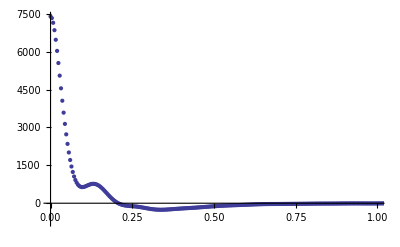

```mathematica
ListPlot[Ct,PlotRange-> {{0,1},{-.1*c1,1*c1}}]
```

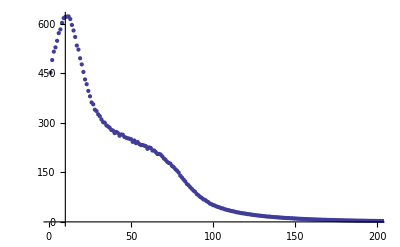

```mathematica
ListPlot[ gT,PlotRange->{{1,200},All}](* FourierParameters a=1 means no normalization
Fourier(b=1)+Fourier(b=-1) to get integral from -inf..inf 
Chop to remove 0 imaginary part*)
```

```mathematica
Export[Inp[[nInput,1]]<>".fft",gT,"Table"]
```

c:\Users\rschulz\Documents\work\lignin_entropie\water\rot300_0.dat.fft

```mathematica
Dimensions[gT]
```

{2501}

```mathematica
j[f_,y_]:=2*y^3*f^3-(y+6y^2)*f^2+(2+6y)*f-2
```

```mathematica
h1[f_,D_]:=j[f,(f/D)^(3/2)]
```

```mathematica
PowerExpand[h1[f,D],D]
```

-2+(2 f^(15/2))/D^(9/2)+f (2+(6 f^(3/2))/D^(3/2))-f^2 (f^(3/2)/D^(3/2)+(6 f^3)/D^3)

```mathematica
rho=nMol/Inp[[nInput,3]]
```

32.7404

```mathematica
m=18.0153
```

18.0153

```mathematica
De=2*gT[[1]]/9/nMol*(Pi*k*T/m)^(1/2)*rho^(1/3)*(6/Pi)^(2/3)
```

0.378265

```mathematica
f1=f/.ToRules[Reduce[h1[f,De]==0,f,Reals]]
```

0.358646

```mathematica
gg[w_]:=gT[[1]]/(1+(gT[[1]]*w/(12*f1*nMol))^2)
```

```mathematica
Dw=2*Pi/10
```

π/5

```mathematica
gs[w_]:=gT[[1+w/Dw]]-gg[w]
```

```mathematica
h=0.3990313224
```

0.399031

```mathematica
Sig= (*should this f1 be here (is in Lin2010)*)k*(Log[1/rho/f1*(4*Pi*m*3/2*nMol*k*T/(3*nMol*h^2))^(3/2)]+5/2)
```

0.0936018

```mathematica
z[y_]:=(1+y+y^2-y^3)/(1-y)^3
```

```mathematica
fy=f1*(f1/De)^(3/2)
```

0.33111

```mathematica
SHs=Sig+k*(Log[z[fy]]+fy*(3*fy-4)/(1-fy)^2)
```

0.0879559

```mathematica
y=f1^(5/2)/De^(3/2)
```

0.33111

```mathematica
vol=Inp[[nInput,3]]
```

30.1768

```mathematica
k(5/2+Log[(2Pi m k T/h^2)^(3/2)vol/f1/nMol*z[y]]+y(3y-4)/(1-y)^2)
```

0.0879559

```mathematica
Wgs=1/3*SHs/k
```

3.5262

```mathematica
hb=h/2/Pi
```

0.0635078

```mathematica
beta=1/k/T
```

0.400906

```mathematica
Who[w_]=beta*hb*w/(Exp[beta*hb*w]-1)-Log[1-Exp[-beta*hb*w]]
```

(0.0254606 w)/(-1+ⅇ^(0.0254606 w))-Log[1-ⅇ^(-0.0254606 w)]

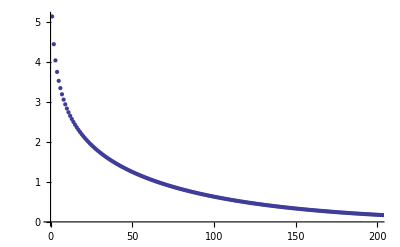

```mathematica
ListPlot[Table[Who[w],{w,Dw,1/.008*2*Pi,Dw}],PlotRange->{{0,200},All}]
```

```mathematica
Svib=k*Sum[Dw/2/Pi*gs[w]*Who[w],{w,Dw,1/.008*2*Pi,Dw}]/nMol
```

0.0255759

0.0255759

0.0255759

```mathematica
Sconf=k*Sum[Dw/2/Pi*gg[w]*Wgs,{w,0,1/.008*2*Pi,Dw}]/nMol
```

0.0321035

```mathematica
(Svib+Sconf)*1000
```

57.6793

```mathematica
Srot=.04448*T/4.1
```

3.25463

```mathematica
.11*4.1/300*1000
```

1.50333

```mathematica
-39245.5/4.1/nMol
```

-9.68833

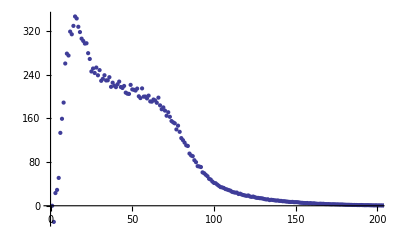

```mathematica
ListPlot[Table[gs[w],{w,0,1/.008*2*Pi,Dw}],PlotRange->{{0,200},All}]
```

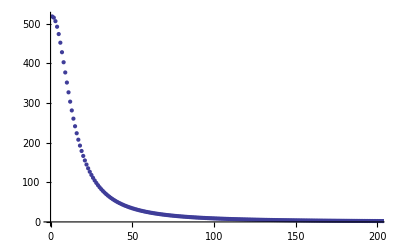

```mathematica
ListPlot[Table[gg[w],{w,0,1/.008*2Pi,Dw}],PlotRange->{{0,200},All}]
```

```mathematica
k*T*gT[[1]]/12/m/nMol
```

0.00604711

```mathematica
Sig*T
```

28.0805

```mathematica
3/2*nMol*k*T
```

3696.63